## ChristoffelVels.nb run common_funs.nb, ChooseTmat.nb, then this notebook θ: azimuthal angle [0, 2π] ϕ: polar angle [0, π]

```mathematica
PrintFigures=False;
```

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
otag=FileNameJoin[{odir,"ChristoffelVels_"}]
```

## Choose your elastic map (and density)

```mathematica
Tmat=TmatBrownAn00;
```

```mathematica
Tmat= TmatFrancois;
```

```mathematica
Tmat= TmatIgel;
```

```mathematica
Tmat= TmatBrownlee[[57]];
```

```mathematica
Tmat= TmatBrownlee[[36]];
```

## Module of functions for calculating anisotropy percentages from elastic maps

#### note 1: the TP label is for input arguments theta (azimuthal angle) and phi (polar angle) note 2: the input map for ChristoffelMatrix needs to be Cmat, not Tmat

```mathematica
ChristoffelMatrixTP[θ_,ϕ_,Tmat_]:=ChristoffelMatrix[xyzTP[{θ,ϕ}],CmatOfTmat[Tmat]];
EigenvaluesOfChristoffelMatrixTP[θ_,ϕ_,Tmat_]:=Eigenvalues[ChristoffelMatrixTP[θ,ϕ,Tmat]];
EigenvaluesOfChristoffelMatrix[{x_,y_,z_},Tmat_]:=Eigenvalues[ChristoffelMatrix[{x,y,z},CmatOfTmat[Tmat]]];
```

#### velocities for closest ISO, km/s (assumes Cij in GPa and density in kg/m^3) note: the input for VPofTmatISO is Tmat, not Cmat; κofTmatISO and μofTmatISO are in common_funs.nb

```mathematica
VPofTmatISO[TmatISO_,density_]:=√(((κofTmatISO[TmatISO]+4/3 μofTmatISO[TmatISO])10^9)/density)/10^3
VSofTmatISO[TmatISO_,density_]:=√((μofTmatISO[TmatISO] 10^9)/density)/10^3
```

```mathematica
VPofTmat[Tmat_]:=VPofTmatISO[Closest[Tmat,ISO],density[Tmat]]
VSofTmat[Tmat_]:=VSofTmatISO[Closest[Tmat,ISO],density[Tmat]]
```

#### get velocities from eigenvalues of Christoffel matrix note: assumes Cij (and eigenvalues) in GPa, density in kg/m3, velocities in km/s

```mathematica
velEig[eigs_,density_]:=√((eigs 10^9)/density)/1000
```

```mathematica
velsTP[θ_,ϕ_,Tmat_,density_]:=√((EigenvaluesOfChristoffelMatrixTP[θ,ϕ,Tmat] 10^9)/density)/1000 
vels[{x_,y_,z_},Tmat_,density_]:=√((EigenvaluesOfChristoffelMatrix[{x,y,z},Tmat] 10^9)/density)/1000
```

#### get eigenvalues of Christoffel matrix note: the idea here is to limit the number of times to call Eigenvalues[] note: Even though Mathematica will reverse sort the eigenvalues, it turns out that we have to apply ReverseSort for cases when a function is being minimized or maximized. note: We also need to ensure that the eigenvalues are DECIMAL, so we apply N[Tmat].

```mathematica
EigList[θ_,ϕ_,Tmat_]:=ReverseSort[EigenvaluesOfChristoffelMatrixTP[θ,ϕ,N[Tmat]]]
E1[θ_,ϕ_,Tmat_]:=EigList[θ,ϕ,Tmat][[1]]
E2[θ_,ϕ_,Tmat_]:=EigList[θ,ϕ,Tmat][[2]]
E3[θ_,ϕ_,Tmat_]:=EigList[θ,ϕ,Tmat][[3]]
```

```mathematica
V1[θ_,ϕ_,Tmat_]:=velEig[E1[θ,ϕ,Tmat],density[Tmat]]
V2[θ_,ϕ_,Tmat_]:=velEig[E2[θ,ϕ,Tmat],density[Tmat]]
V3[θ_,ϕ_,Tmat_]:=velEig[E3[θ,ϕ,Tmat],density[Tmat]]
```

#### example of why entries need to be decimal, prior to sorting

```mathematica
Sort[{1,1-√(4/3)}]
Sort[{1,1.-√(4/3)}]
```

#### numerical integration on the sphere to get the spherical average

```mathematica
pg=3;ag=3;
MeanSphere[f_,Tmat_]:=1/(4 π)NIntegrate[f[θ,ϕ,Tmat]Sin[ϕ],{θ,0,2π},{ϕ,0,π},AccuracyGoal->ag,PrecisionGoal->pg];
L2norm[f_,Tmat_]:=√(1/(4 π)NIntegrate[f[θ,ϕ,Tmat]^2 Sin[ϕ],{θ,0,2π},{ϕ,0,π},AccuracyGoal->ag,PrecisionGoal->pg]);
E1mean[Tmat_]:=MeanSphere[E1,Tmat];
E2mean[Tmat_]:=MeanSphere[E2,Tmat];
E3mean[Tmat_]:=MeanSphere[E3,Tmat];
Emean[Tmat_]:=Emean[Tmat]={E1mean[Tmat],E2mean[Tmat],E3mean[Tmat]};
```

#### brute-force approach, starting with uniformly distributed points on the sphere

```mathematica
(*nrand=10000;
θrand=Table[2 Pi RandomReal[],nrand];
ϕrand=Table[ArcCos[RandomReal[{-1,1}]],nrand];
ListPlot[Transpose[{θrand,ϕrand}],AxesLabel->{"θ","ϕ"},Frame->True,PlotRange->{{0,2Pi},{0,Pi}}]
vals=Table[E1[θrand[[i]],ϕrand[[i]],Tmat],{i,nrand}];
Mean[vals]
Median[vals]*)
```

#### dots colored by function value

```mathematica
(*ListPlot[Style[{#1,#2},ColorData["Rainbow"][#3]]&@@@Transpose[{θrand,ϕrand,Rescale[vals]}],AxesLabel->{"θ","ϕ"},Frame->True,PlotRange->{{0,2 Pi},{0,Pi}},PlotLabel->"Colored Scatterplot of θ and ϕ",PlotLegends->BarLegend[{"Rainbow",{Min[vals],Max[vals]}}]]*)
```

#### continuous contour plot

```mathematica
(*ContourPlot[E1[θ,ϕ,Tmat],{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic]*)
```

#### helper function for extracting numbers from the minimize/maximize

```mathematica
ExtractValues[optResult_]:={optResult[[1]],optResult[[2,1,2]],optResult[[2,2,2]]}
```

#### numerical minimization/maximization to find min/max eigenvalues

```mathematica
(* Clear[FindMaxMinEigenvalues,Emax,Emin,θmax,θmin,ϕmax,ϕmin] *)
```

```mathematica
(*Clear[nmaximizeE1,nminimizeE1,nmaximizeE2,nminimizeE2,nmaximizeE3,nminimizeE3];*)
```

```mathematica
(* Clear[θ,ϕ]; *)
```

```mathematica
nmaximizeE1[Tmat_]:=nmaximizeE1[Tmat]=NMaximize[{E1[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
nminimizeE1[Tmat_]:=nminimizeE1[Tmat]=NMinimize[{E1[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
nmaximizeE2[Tmat_]:=nmaximizeE2[Tmat]=NMaximize[{E2[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
nminimizeE2[Tmat_]:=nminimizeE2[Tmat]=NMinimize[{E2[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
nmaximizeE3[Tmat_]:=nmaximizeE3[Tmat]=NMaximize[{E3[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
nminimizeE3[Tmat_]:=nminimizeE3[Tmat]=NMinimize[{E3[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
```

```mathematica
E1max[Tmat_]:=nmaximizeE1[Tmat][[1]];
E1maxθ[Tmat_]:=nmaximizeE1[Tmat][[2,1,2]];
E1maxϕ[Tmat_]:=nmaximizeE1[Tmat][[2,2,2]];
E2max[Tmat_]:=nmaximizeE2[Tmat][[1]];
E2maxθ[Tmat_]:=nmaximizeE2[Tmat][[2,1,2]];
E2maxϕ[Tmat_]:=nmaximizeE2[Tmat][[2,2,2]];
E3max[Tmat_]:=nmaximizeE3[Tmat][[1]];
E3maxθ[Tmat_]:=nmaximizeE3[Tmat][[2,1,2]];
E3maxϕ[Tmat_]:=nmaximizeE3[Tmat][[2,2,2]];
```

```mathematica
E1min[Tmat_]:=nminimizeE1[Tmat][[1]];
E1minθ[Tmat_]:=nminimizeE1[Tmat][[2,1,2]];
E1minϕ[Tmat_]:=nminimizeE1[Tmat][[2,2,2]];
E2min[Tmat_]:=nminimizeE2[Tmat][[1]];
E2minθ[Tmat_]:=nminimizeE2[Tmat][[2,1,2]];
E2minϕ[Tmat_]:=nminimizeE2[Tmat][[2,2,2]];
E3min[Tmat_]:=nminimizeE3[Tmat][[1]];
E3minθ[Tmat_]:=nminimizeE3[Tmat][[2,1,2]];
E3minϕ[Tmat_]:=nminimizeE3[Tmat][[2,2,2]];
```

```mathematica
Emax[Tmat_]:={E1max[Tmat],E2max[Tmat],E3max[Tmat]};
Emin[Tmat_]:={E1min[Tmat],E2min[Tmat],E3min[Tmat]};
θmax[Tmat_]:={E1maxθ[Tmat],E2maxθ[Tmat],E3maxθ[Tmat]};
θmin[Tmat_]:={E1minθ[Tmat],E2minθ[Tmat],E3minθ[Tmat]};
ϕmax[Tmat_]:={E1maxϕ[Tmat],E2maxϕ[Tmat],E3maxϕ[Tmat]};
ϕmin[Tmat_]:={E1minϕ[Tmat],E2minϕ[Tmat],E3minϕ[Tmat]};
```

```mathematica
FindMaxMinEigenvalues[Tmat_]:={Emax[Tmat],Emin[Tmat],θmax[Tmat],θmin[Tmat],ϕmax[Tmat],ϕmin[Tmat]};
```

#### formatted text for output and plotting

```mathematica
sfmt[x_]:=NumberForm[Chop[x,0.001],{Infinity,2}];
strmax[Tmat_,k_]:=Style[Row[{"E",k,"max = ",sfmt[Emax[Tmat][[k]]]," at (θ,ϕ) = (",sfmt[θmax[Tmat][[k]]],", ",sfmt[ϕmax[Tmat][[k]]],")"}]];
strmin[Tmat_,k_]:=Style[Row[{"E",k,"min = ",sfmt[Emin[Tmat][[k]]]," at (θ,ϕ) = (",sfmt[θmin[Tmat][[k]]],", ",sfmt[ϕmin[Tmat][[k]]],")"}]];
strmean[Tmat_,k_]:=Style[Row[{"E",k,"mean = ",sfmt[Emean[Tmat][[k]]], ", (E",k,"min+E",k,"max)/2 = ",sfmt[(Emin[Tmat][[k]]+Emax[Tmat][[k]])/2]}]];
PrintEigs[Tmat_]:=Module[{i},
Print["Summary of eigenvalues:"];
Do[Print["   " <>ToString[strmax[Tmat,i]]];
Print["   " <>ToString[strmin[Tmat,i]]];
Print["   " <>ToString[strmean[Tmat,i]]];
,{i,1,3}];];
```

#### contour plots of eigenvalues

```mathematica
(* ContourPlot[E1[θ,ϕ,TmatBrownAn00],{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic] *)
```

```mathematica
PlotEig[Tmat_,k_]:=ContourPlot[EigenvaluesOfChristoffelMatrixTP[θ,ϕ,Tmat][[k]],{θ,0,2 π},{ϕ,0,π},
PlotRange->Automatic,AspectRatio->Automatic,PlotLegends->Automatic,
Epilog->{Red,PointSize[Large],Point[{θmax[Tmat][[k]],ϕmax[Tmat][[k]]}],Green,PointSize[Large],Point[{θmin[Tmat][[k]],ϕmin[Tmat][[k]]}]},
PlotLabel->Style[ToString[strmax[Tmat,k]]<>", "<>ToString[strmin[Tmat,k]],FontSize->12,Black],ImageSize->500]
```

#### velocities, km/s

```mathematica
Clear[Vmax,Vmin,Vmean,VPaniso,VSaniso,VSmin,VSmax]
```

```mathematica
Vmax[Tmat_]:=velEig[Emax[Tmat],density[Tmat]]
Vmin[Tmat_]:=velEig[Emin[Tmat],density[Tmat]]
Vmean[Tmat_]:=velEig[Emean[Tmat],density[Tmat]]
```

```mathematica
V23diff[θ_,ϕ_,Tmat_]:=V2[θ,ϕ,Tmat]-V3[θ,ϕ,Tmat]
V23mean[θ_,ϕ_,Tmat_]:=(V2[θ,ϕ,Tmat]+V3[θ,ϕ,Tmat])/2
V23aniso[θ_,ϕ_,Tmat_]:=100V23diff[θ,ϕ,Tmat]/V23mean[θ,ϕ,Tmat]
```

```mathematica
nmaximizeV23aniso[Tmat_]:=nmaximizeV23aniso[Tmat]=NMaximize[{V23aniso[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"];
V23anisoMax[Tmat_]:=nmaximizeV23aniso[Tmat][[1]];
θV23anisoMax[Tmat_]:=nmaximizeV23aniso[Tmat][[2,1,2]];
ϕV23anisoMax[Tmat_]:=nmaximizeV23aniso[Tmat][[2,2,2]];
strV23[Tmat_]:=Style[Row[{"Max[ 100(v2-v3) / ((v2+v3)/2) ] = ",sfmt[V23anisoMax[Tmat]],
" at (θ,ϕ) = (",sfmt[θV23anisoMax[Tmat]],", ",sfmt[ϕV23anisoMax[Tmat]],")"}]];
```

#### anisotropy note the choice of denominator, which we take as (vmin+vmax)/2

```mathematica
Vaniso[vmin_,vmax_,vdenom_]:=100(vmax-vmin)/vdenom
```

```mathematica
VPmin[Tmat_]:=Vmin[Tmat][[1]];
VPmax[Tmat_]:=Vmax[Tmat][[1]];
VPdenom1[Tmat_]:=VPofTmat[Tmat];
VPdenom2[Tmat_]:=(VPmin[Tmat]+VPmax[Tmat])/2;
VPdenom[Tmat_]:=VPdenom2[Tmat]
VPaniso[Tmat_]:=Vaniso[VPmin[Tmat],VPmax[Tmat],VPdenom[Tmat]];
```

```mathematica
VSmin[Tmat_]:=Min[Vmin[Tmat][[{2,3}]]];
VSmax[Tmat_]:=Max[Vmax[Tmat][[{2,3}]]];
V23mean[vels_]:=Mean[vels[[{2,3}]]]
VSdenom1[Tmat_]:=VSofTmat[Tmat];
VSdenom2[Tmat_]:=(VSmin[Tmat]+VSmax[Tmat])/2;
VSdenom[Tmat_]:=VSdenom2[Tmat]
VSaniso[Tmat_]:=Vaniso[VSmin[Tmat],VSmax[Tmat],VSdenom[Tmat]]
```

```mathematica
PrintVels[Tmat_]:=Module[{vmax,vmin,vmean,vp0,vs0},
vmax=Vmax[Tmat];
vmin=Vmin[Tmat];
vp0=VPofTmat[Tmat];
vs0=VSofTmat[Tmat];
vmean=Vmean[Tmat];
Print["Summary of velocity values:"];
Print["   density = ",density[Tmat]];
Print["   vmax = ",vmax];
Print["   vmin = ",vmin];
Print["   vmax - vmin = ",vmax-vmin];
Print["   (vmin + vmax)/2 = ",(vmin + vmax)/2];
Print["   vmean = ",vmean];
Print["   {vp0, vs0, vs0} = ",N[{vp0,vs0,vs0}]];
Print["   100 (vmax - vmin) / (vmin + vmax)/2 = ",Vaniso[vmin,vmax,(vmin+vmax)/2]," (v2+v3)/2 = ",V23mean[Vaniso[vmin,vmax,(vmin+vmax)/2]]];
Print["   100 (vmax - vmin) / vmean = ",Vaniso[vmin,vmax,vmean]," (v2+v3)/2 = ",V23mean[Vaniso[vmin,vmax,vmean]]];
Print["   100 (vmax - vmin) / v0 = ",Vaniso[vmin,vmax,{vp0,vs0,vs0}]," (v2+v3)/2 = ",V23mean[Vaniso[vmin,vmax,{vp0,vs0,vs0}]]];
Print["   v1max - v1min = ",vmax[[1]]," - ",vmin[[1]]," = ",vmax[[1]]-vmin[[1]]];
Print["   v2max - v3min = ",vmax[[2]]," - ",vmin[[3]]," = ",vmax[[2]]-vmin[[3]]];
Print["   VPaniso = 100 (v1max - v1min) / ((v1max + v1min)/2) = ",VPaniso[Tmat]];
Print["   VSaniso = 100 (v2max - v3min) / ((v2max + v3min)/2) = ",VSaniso[Tmat]];
Print["   " <>ToString[strV23[Tmat]]];
Print["   βISO = ",βT[Tmat,ISO]/Degree," degrees, dISO = ",dT[Tmat,ISO]," GPa"];
];
```

## Example: Brownlee36

```mathematica
(*MatrixNote[Tmat]
PrintVoigt[Tmat]
TISO=Closest[Tmat,ISO];
Print["The closest isotropic map in Voigt notation is ",DispMat[CmatOfTmat[TISO]]]
AngleMatrix[Tmat,TISO]/Degree*)
```

```mathematica
(*PrintEigs[Tmat]*)
```

```mathematica
MatrixNote[Tmat]
PrintVels[Tmat]
```

```mathematica
Vbrownlee[θ_,ϕ_,Tmat_]:=1/V3[θ,ϕ,Tmat]-1/V2[θ,ϕ,Tmat]
```

#### contour plots (min/max could be added)

```mathematica
Plotf[f_,stlab_]:=ContourPlot[f[θ,ϕ,Tmat],{θ,0,2π},{ϕ,0,π},PlotRange->All,AspectRatio->Automatic,PlotLegends->Automatic,PlotLabel->stlab]
```

```mathematica
(*Plotf[V1,"V1, km/s"]
Plotf[V2,"V2, km/s"]
Plotf[V3,"V3, km/s"]
Plotf[V23mean,"(V2+V3)/2, km/s"]
Plotf[V23diff,"V2-V3, km/s"]
Plotf[V23aniso,"100(V2-V3) / ((V2+V3)/2), percent"]
Plotf[Vbrownlee,"1/V3 - 1/V2, s/km"]*)
```

#### From Sarah Brownlee: For tensor 36 my calculations are: AVp: 34.6971 where AVp = (Vpmax - Vpmin)/(0.5(Vpmax + Vpmin)) * 100 AVsMax: 22.4719 where AVsMax = max(Vs1 - Vs2)/(0.5(Vs1max + Vs1min)) * 100 DVsMax: 0.070317 where DVsMax = max(1/Vs2 - 1/Vs1)

#### DVsMax (requires maximization) note: Max[ 100(v2-v3) / ((v2+v3)/2) ] = 23.26 at (θ,ϕ) = (2.46, 1.47)

```mathematica
(*nums=NMaximize[{Vbrownlee[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"]
{dmx,thmx,phmx}=ExtractValues[nums]
Vbrownlee[thmx,phmx,Tmat]*)
```

#### Vs1 - Vs2 (requires maximization) note: Max[ 100(v2-v3) / ((v2+v3)/2) ] = 23.26 at (θ,ϕ) = (2.46, 1.47)

```mathematica
(*nums=NMaximize[{V23diff[θ,ϕ,Tmat],0<=θ<2 π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"]
{dmx,thmx,phmx}=ExtractValues[nums]
V23diff[thmx,phmx,Tmat]*)
```

#### AVsMax

```mathematica
(*V23diff[thmx,phmx,Tmat]
Vmax[Tmat]
Vmin[Tmat]
(Vmax[Tmat][[2]]+Vmin[Tmat][[2]])/2
100 V23diff[thmx,phmx,Tmat]/((Vmax[Tmat][[2]]+Vmin[Tmat][[2]])/2)*)
```

## Example

#### display output

```mathematica
PrintVoigt[N[Tmat]]
Print["The closest ISO map [Voigt] is ",DispMat[CmatOfTmat[Closest[Tmat,ISO]],1]]
```

#### display the closest-ISO map

```mathematica
TmatISO=Closest[Tmat,ISO];
CmatISO=CmatOfTmat[TmatISO];
MatrixForm[CmatISO]
```

#### test values

```mathematica
θx=33.63 Degree;
ϕx=119.22 Degree;
EigList[θx,ϕx,Tmat]
E1[θx,ϕx,Tmat]
E2[θx,ϕx,Tmat]
E3[θx,ϕx,Tmat]
```

#### this will determine Emax, Emin, etc

```mathematica
FindMaxMinEigenvalues[Tmat]
```

```mathematica
PrintEigs[Tmat]
```

#### contour plots showing the minimum (green) and maximum (red) for E1, E2, E3

```mathematica
(*PlotEig[Tmat,1]
PlotEig[Tmat,2]
PlotEig[Tmat,3]*)
```

#### check minimization for Igel E2

```mathematica
(* PlotEig[Tmat,2]
NMaximize[{E2[θ,ϕ,Tmat],0<=θ<2π,0<=ϕ<=π},{θ,ϕ},Method->"RandomSearch"]
NMaximize[{E2[θ,ϕ,Tmat],3<=θ<4,2<=ϕ<=3},{θ,ϕ},Method->"RandomSearch"] *)
```

#### overall max and min velocities (needed for legend and contours)

```mathematica
Max[Vmax[Tmat]]
Min[Vmin[Tmat]]
```

```mathematica
PrintVels[Tmat]
```

## Brownlee et al. (2017) database

#### histogram of βISO

```mathematica
pβISO =N[βT[#,ISO]]/Degree&/@TmatBrownlee;
pνISO =PoissonOfTmatISO[Closest[#,ISO]]&/@TmatBrownlee;
```

```mathematica
Histogram[pβISO,Automatic,"Count",AxesLabel->{None,None},ImageSize->Large,Frame->True,FrameLabel->{Style[Row[{Subscript["β","ISO"],", degrees"}],FontSize->14,Black],Style["Counts",FontSize->14,Black]},FrameTicks->{Automatic,Automatic},FrameStyle->Black,LabelStyle->Directive[Black,FontSize->14],PlotTheme->"Detailed",PlotLabel->Style["Brownlee et al. (2017) database of "<>ToString[Length[pβISO]]<>" elastic tensors",FontSize->14,Black]]
Histogram[pνISO,Automatic,"Count",AxesLabel->{None,None},ImageSize->Large,Frame->True,FrameLabel->{Style[Row[{Subscript["ν","ISO"]}],FontSize->14,Black],Style["Counts",FontSize->14,Black]},FrameTicks->{Automatic,Automatic},FrameStyle->Black,LabelStyle->Directive[Black,FontSize->14],PlotTheme->"Detailed",PlotLabel->Style["Brownlee et al. (2017) database of "<>ToString[Length[pβISO]]<>" elastic tensors",FontSize->14,Black]]
```

```mathematica
(*TmatTable[TmatBrownlee]*)
```

## Run for a full set of maps (see ChooseTmat.nb)

```mathematica
stlab="";
```

```mathematica
TmatAll={TmatBrownAn00,TmatVestrum,TmatFrancois,TmatBrownAn96};
```

```mathematica
TmatAll=Take[TmatZenodoAlphabetical,{1,4}];
```

#### Option B: adjust in ChooseTmat, then select an appropriate stlab

```mathematica
(*stlab="Zenodo";
stlab="Earth";
stlab="All";
ShowPert=True;
TmatAll=Join[TmatChoose,TmatChoosePertN];
slopeVPbetaR = 3.4;slopeVPbetaB = 1.5;
slopeVSbetaR = 1.5;slopeVSbetaB = 6.5;
slopeVSVPR=0.6; slopeVSVPB=4;*)
```

#### Option A: choose a set without showing the perturbed versions

```mathematica
ShowPert=False;
TmatAll=TmatBrownlee;stlab="Brownlee";
slopeVPbetaR = 2.4;slopeVPbetaB = 1.7;
slopeVSbetaR = 1.6;slopeVSbetaB = 2.8;
slopeVSVPR=0.6; slopeVSVPB=1.8;
```

```mathematica
ShowPert=False;
TmatAll=TmatZenodoAlphabetical;stlab="Zenodo";
slopeVPbetaR = 2.4;slopeVPbetaB = 1.3;
slopeVSbetaR = 1.8;slopeVSbetaB = 4.2;
slopeVSVPR=0.6 ;slopeVSVPB=2.8;
```

```mathematica
ShowPert=False;
TmatAll=Tmatall;stlab="All";
slopeVPbetaR = 2.4;slopeVPbetaB = 1.3;
slopeVSbetaR = 1.8;slopeVSbetaB = 4.2;
slopeVSVPR=0.6 ;slopeVSVPB=2.8;
```

```mathematica
ShowPert=False;
TmatAll=TmatEarth;stlab="Earth";
slopeVPbetaR = 2.4;slopeVPbetaB = 1.65;
slopeVSbetaR = 1.5;slopeVSbetaB = 3.7;
slopeVSVPR=0.55 ;slopeVSVPB=1.9;
slopeVSVSR=1;slopeVSVSB=0.7;
```

```mathematica
Length[TmatAll]
```

```mathematica
(*TmatTable[TmatAll]*)
```

#### calculate anisotropy for each map

```mathematica
Do[Tmatx=TmatAll[[i]];
Print[Style[StringJoin["Elastic map ",ToString[i]," / ",ToString[Length[TmatAll]]," : ",Tlab[Tmatx]," [",MatrixShortNote[Tmatx],"]"],Bold]];
FindMaxMinEigenvalues[Tmatx];
PrintEigs[Tmatx];
PrintVels[Tmatx];,{i,Length[TmatAll]}]
```

#### choose one map

```mathematica
(*i=First[Flatten[Position[TmatAll,TmatBrownAn00]]]*)
i=1
MatrixForm[TmatAll[[i]]]
MatrixNote[TmatAll[[i]]]
PrintEigs[TmatAll[[i]]]
PrintVels[TmatAll[[i]]]
```

```mathematica
(*i=36;
Tmat=TmatAll[[i]];
Print[Style[StringJoin["Elastic map ",ToString[i]," / ",ToString[Length[TmatAll]]," : ",Tlab[Tmat]," [",MatrixShortNote[Tmat],"]"],Bold]];
FindMaxMinEigenvalues[Tmat];
PrintEigs[Tmat];
PrintVels[Tmat];*)
```

#### display the saved values in a table

```mathematica
fmt[x_]:=NumberForm[Chop[x,0.001],{Infinity,2}]
generateRow[Tmat_,ii_]:={ii,Tlab[Tmat],MatrixShortNote[Tmat],fmt[density[Tmat]],fmt/@Emax[Tmat],fmt/@Emin[Tmat],fmt/@θmax[Tmat],fmt/@θmin[Tmat],fmt/@ϕmax[Tmat],fmt/@ϕmin[Tmat],fmt/@Vmax[Tmat],fmt/@Vmin[Tmat],fmt/@Vmean[Tmat],N[PoissonOfTmatISO[Closest[Tmat,ISO]]],fmt[N[VPofTmat[Tmat]]],fmt[N[VSofTmat[Tmat]]],fmt[VPaniso[Tmat]],fmt[ VSaniso[Tmat]]}
tableData=Prepend[Table[generateRow[TmatAll[[i]],i],{i,Length[TmatAll]}],
{"","","","rho","Emax","Emin","θmax","θmin","ϕmax","ϕmin","Vmax","Vmin","Vmean","nu0","VP0","VS0","VPaniso","VSaniso"}];
TableForm[tableData,TableHeadings->{None,None}]
```

#### subset of rows and columns

```mathematica
imin=1;imax=imin;
generateRowShort[Tmat_,ii_]:={ii,Tlab[Tmat],MatrixShortNote[Tmat],fmt[density[Tmat]],fmt/@Emax[Tmat],fmt/@Emin[Tmat],fmt/@Vmax[Tmat],fmt/@Vmin[Tmat],fmt/@Vmean[Tmat],N[PoissonOfTmatISO[Closest[Tmat,ISO]]],fmt[N[VPofTmat[Tmat]]],fmt[N[VSofTmat[Tmat]]],fmt[VPaniso[Tmat]],fmt[ VSaniso[Tmat]]}
tableDataShort=Prepend[Table[generateRowShort[TmatAll[[i]],i],{i,imin,imax}],{"","","","rho","Emax","Emin","Vmax","Vmin","Vmean","nu0","VP0","VS0","VPaniso","VSaniso"}];
TableForm[tableDataShort,TableHeadings->{None,None}]
```

#### save three values: VPaniso, VSaniso, betaISO

```mathematica
pVp=VPaniso[#]&/@TmatAll;
pVs= VSaniso[#]&/@TmatAll;
pVsDir= V23anisoMax[#]&/@TmatAll;
pβISO =N[βT[#,ISO]]/Degree&/@TmatAll;
tlabs =MatrixShortNote[#]&/@TmatAll
```

#### plot first half of points in black second half in red

```mathematica
If[ShowPert,isplit=Floor[Length[pβISO]/2],isplit=Length[pβISO]]
```

#### plot text labels

```mathematica
title=StringJoin[stlab," elastic maps [",ToString[isplit],"]"]
stslope[xA_,xB_]:= "  ("<>ToString[xA]<>", "<>ToString[xB]<>")"
```

#### axis limits for zoomed-in versions

```mathematica
ShowTextLabels=True;
zvpmax=17;
zvsmax=22;
zbetamax=10;
```

#### define scatterplots

```mathematica
otag2:=otag<>stlab<>"_Pert"<>ToString[Boole[ShowPert]]<>"_TextLabels"<>ToString[Boole[ShowTextLabels]]<>"_plot"
```

```mathematica
pmax=Max[pβISO];
plot1[prange_]:=ListPlot[Transpose[{pβISO,pVp}],PlotStyle->None,Frame->True,
FrameLabel->{Style["betaISO, degrees",FontSize->16,Black],Style["Vp anisotropy, %",FontSize->16,Black]},
FrameTicksStyle->Directive[FontSize->14,Black],
Epilog->{If[ShowTextLabels,Table[Text[Style[tlabs[[i]],FontSize->12],{pβISO[[i]],pVp[[i]]},{0,-1}],{i,Length[pβISO]}]],
If[ShowPert,{Table[{Red,PointSize[0.01],Point[{pβISO[[i]],pVp[[i]]}]},{i,isplit+1,Length[pβISO]}],
Table[{Black,PointSize[0.01],Point[{pβISO[[i]],pVp[[i]]}]},{i,1,isplit}]},
Table[{Black,PointSize[0.01],Point[{pβISO[[i]],pVp[[i]]}]},{i,Length[pβISO]}]],
{Red,Dashed,Line[{{0,0},{pmax,slopeVPbetaR pmax}}]},{Blue,Dashed,Line[{{0,0},{Max[pβISO],slopeVPbetaB Max[pβISO]}}]}},PlotLabel->Style[title<>stslope[slopeVPbetaB,slopeVPbetaR],FontSize->16,Black],GridLines->Automatic,PlotRange->prange,ImageSize->600]
p1:=GraphicsRow[{plot1[All],plot1[{{0,zbetamax},{0,zvpmax}}]},Spacings->0,ImageSize->1200];
```

```mathematica
pmax=Max[pβISO];
plot2[prange_]:=ListPlot[Transpose[{pβISO,pVs}],PlotStyle->None,Frame->True,
FrameLabel->{Style["betaISO, degrees",FontSize->16,Black],Style["Vs anisotropy, %",FontSize->16,Black]},
FrameTicksStyle->Directive[FontSize->14,Black],
Epilog->{If[ShowTextLabels,Table[Text[Style[tlabs[[i]],FontSize->12],{pβISO[[i]],pVs[[i]]},{0,-1}],{i,Length[pβISO]}]],
If[ShowPert,{Table[{Red,PointSize[0.01],Point[{pβISO[[i]],pVs[[i]]}]},{i,isplit+1,Length[pβISO]}],
Table[{Black,PointSize[0.01],Point[{pβISO[[i]],pVs[[i]]}]},{i,1,isplit}]},
Table[{PointSize[0.01],Point[{pβISO[[i]],pVs[[i]]}]},{i,Length[pβISO]}]],
{Red,Dashed,Line[{{0,0},{pmax,slopeVSbetaR pmax}}]},
{Blue,Dashed,Line[{{0,0},{pmax,slopeVSbetaB pmax}}]}},
PlotLabel->Style[title<> stslope[slopeVSbetaR,slopeVSbetaB],FontSize->16,Black],
GridLines->Automatic,PlotRange->prange,ImageSize->600]
p2:=GraphicsRow[{plot2[All],plot2[{{0,zbetamax},{0,zvsmax}}]},Spacings->0,ImageSize->1200];
```

```mathematica
pmax=1.05 Max[Join[pVp,pVs]];
pmax=Max[pVp];
plot3[prange_]:=ListPlot[Transpose[{pVp,pVs}],PlotStyle->None,Frame->True,
FrameLabel->{Style["Vp anisotropy, %",FontSize->16,Black],Style["Vs anisotropy, %",FontSize->16,Black]},
FrameTicksStyle->Directive[FontSize->14,Black],
Epilog->{If[ShowTextLabels,Table[Text[Style[tlabs[[i]],FontSize->12],{pVp[[i]],pVs[[i]]},{0,-1}],{i,Length[pVp]}]],
If[ShowPert,{Table[{Red,PointSize[0.01],Point[{pVp[[i]],pVs[[i]]}]},{i,isplit+1,Length[pVp]}],
Table[{Black,PointSize[0.01],Point[{pVp[[i]],pVs[[i]]}]},{i,1,isplit}]},
Table[{PointSize[0.01],Point[{pVp[[i]],pVs[[i]]}]},{i,Length[pVp]}]],
{Dashed,Red,Line[{{0,0},{pmax,slopeVSVPR pmax}}]},
{Dashed,Blue,Line[{{0,0},{pmax,slopeVSVPB pmax}}]}
},
PlotLabel->Style[title<> stslope[slopeVSVPR,slopeVSVPB],FontSize->16,Black],
GridLines->Automatic,PlotRange->prange,AspectRatio->1,ImageSize->600]
p3:=GraphicsRow[{plot3[All],plot3[{{0,zvpmax},{0,zvsmax}}]},Spacings->0,ImageSize->1200];
```

```mathematica
pmax=1.05 Max[Join[pVp,pVsDir]];
pmax=Max[pVp];
plot4[prange_]:=ListPlot[Transpose[{pVp,pVsDir}],PlotStyle->None,Frame->True,FrameLabel->{Style["Vp anisotropy, %",FontSize->16,Black],Style["VsDir anisotropy, %",FontSize->16,Black]},
FrameTicksStyle->Directive[FontSize->14,Black],
Epilog->{If[ShowTextLabels,Table[Text[Style[tlabs[[i]],FontSize->12],{pVp[[i]],pVsDir[[i]]},{0,-1}],{i,Length[pVp]}]],
If[ShowPert,{Table[{Red,PointSize[0.01],Point[{pVp[[i]],pVsDir[[i]]}]},{i,isplit+1,Length[pVp]}],
Table[{Black,PointSize[0.01],Point[{pVp[[i]],pVsDir[[i]]}]},{i,1,isplit}]},
Table[{PointSize[0.01],Point[{pVp[[i]],pVsDir[[i]]}]},{i,Length[pVp]}]],
{Dashed,Red,Line[{{0,0},{pmax,slopeVSVPR pmax}}]},
{Dashed,Blue,Line[{{0,0},{pmax,slopeVSVPB pmax}}]}
},
PlotLabel->Style[title<> stslope[slopeVSVPR,slopeVSVPB],FontSize->16,Black],
GridLines->Automatic,PlotRange->prange,AspectRatio->1,ImageSize->600]
p4:=GraphicsRow[{plot4[All],plot4[{{0,zvpmax},{0,zvsmax}}]},Spacings->0,ImageSize->1200];
```

```mathematica
pmax=Max[pVs];
plot5[prange_]:=ListPlot[Transpose[{pVs,pVsDir}],PlotStyle->None,Frame->True,FrameLabel->{Style["Vs anisotropy, %",FontSize->16,Black],Style["VsDir anisotropy, %",FontSize->16,Black]},
FrameTicksStyle->Directive[FontSize->14,Black],
Epilog->{If[ShowTextLabels,Table[Text[Style[tlabs[[i]],FontSize->12],{pVs[[i]],pVsDir[[i]]},{0,-1}],{i,Length[pVs]}]],
If[ShowPert,{Table[{Red,PointSize[0.01],Point[{pVs[[i]],pVsDir[[i]]}]},{i,isplit+1,Length[pVs]}],
Table[{Black,PointSize[0.01],Point[{pVs[[i]],pVsDir[[i]]}]},{i,1,isplit}]},
Table[{PointSize[0.01],Point[{pVs[[i]],pVsDir[[i]]}]},{i,Length[pVs]}]],
{Dashed,Red,Line[{{0,0},{pmax,slopeVSVSR pmax}}]},
{Dashed,Blue,Line[{{0,0},{pmax,slopeVSVSB pmax}}]}
},
PlotLabel->Style[title<> stslope[slopeVSVSR,slopeVSVSB],FontSize->16,Black],
GridLines->Automatic,PlotRange->prange,AspectRatio->1,ImageSize->600]
p5:=GraphicsRow[{plot5[All],plot5[{{0,zvpmax},{0,zvsmax}}]},Spacings->0,ImageSize->1200];
```

```mathematica
If[PrintFigures,Export[otag2<>"1.pdf",p1],p1]
If[PrintFigures,Export[otag2<>"2.pdf",p2],p2]
If[PrintFigures,Export[otag2<>"3.pdf",p3],p3]
If[PrintFigures,Export[otag2<>"4.pdf",p4],p4]
If[PrintFigures,Export[otag2<>"5.pdf",p5],p5]
```

## Examples

#### Earth

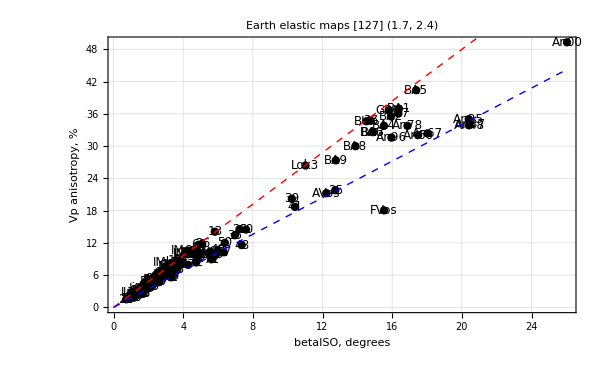
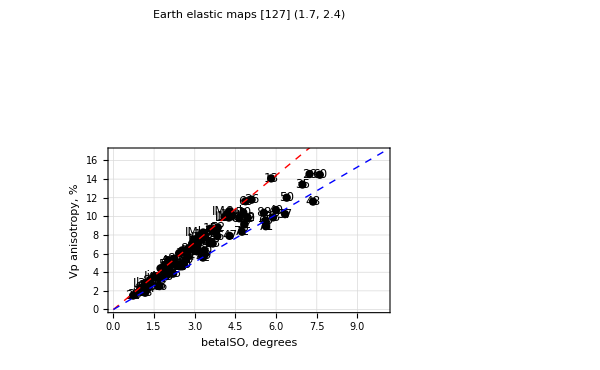

#### Earth - with perturbed versions